```mathematica
ClearAll;

image = -Graphics-;

GetPoints[i_]:=Manipulate[Grid[{{"Mask(add/del alt+click/cmd+click?","Selected Points"},{Show[i,ImageSize->ImageDimensions[i]],mask=Graphics[Disk[#,30]&/@p,PlotRange->Thread[{{1,1},ImageDimensions[i]}],ImageSize->ImageDimensions[i]];
HighlightImage[i,points=ImageKeypoints[i,MaxFeatures->n,Method->method,Masking->mask],ImageSize->ImageDimensions[i]]}}],{{p,{ImageDimensions[i]/2}},Locator,LocatorAutoCreate->True,Appearance->Style["○",Red,90]},{{n,100,"number of points"},10,300,10},{{method,"FAST"},{"AGAST","AKAZE","BRISK","FAST","KAZE","ORB","SURF"},ControlType->RadioButton},ControlPlacement->{Top}]

GetList[i_,points_]:=Module[{},ClearAll[list];list={};
Row[{Manipulate[Grid[{{"Selected Points","Sample List"},{Show[i,Graphics[{Point[u]}],ImageSize->ImageDimensions[i]],Dynamic[If[(ValueQ[list]==False)||(list=={}),"1. move bottom-left and upper-right red points\n2. set each coordinate\n3. add/del points if necessary(alt+click/cmd+click?\n4. click Calculate button",list=Round[#,accuracy]&/@list;
Sort[RandomSample[list,UpTo[10]]]//TableForm]]}}],Row[{Dynamic[u[[1]]],"->",Control[{coordinate1,{{0,0}},InputField,ImageSize->80}],Dynamic[u[[2]]],"->",Control[{coordinate2,{{1,1}},InputField,ImageSize->80}],Control[{{accuracy,0.01},InputField,ImageSize->50}]},"  "],Row[{Button["Calculate",list=locator2coordinate[u,{coordinate1,coordinate2}];,ImageSize->120]},"  "],Row[{Button["Clear points",u=Take[u,2];Put[u,"locator"],ImageSize->120]},"  "],{{u,Join[{{1,1},ImageDimensions[i]-{1,1}},Sort[points]]},Locator,LocatorAutoCreate->True,Appearance->Style["●",Red,8]},ControlPlacement->{Bottom,Bottom}]},"  "]]

locator2coordinate[list_,sample_]:=Module[{a,b,c,d,mat,cnst,solve,matx,cnstx},mat={{a,0},{0,d}};cnst={b,c};
solve=Solve[mat.list[[1]]+cnst==sample[[1]]&&mat.list[[2]]+cnst==sample[[2]],{a,b,c,d}];
matx=mat/.solve;cnstx=cnst/.solve;
Partition[Flatten[(matx.#+cnstx)&/@list],2]//Sort]

fining=image;
GetPoints[fining]
```

```mathematica
GetList[fining,points]
```

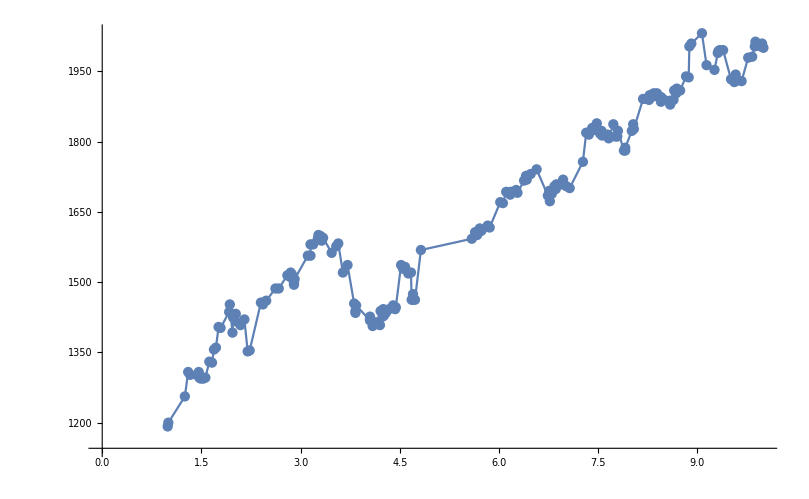
original | calculated
-Graphics- | -Graphics-

```mathematica
i=fining;
Grid[{{"original","calculated"},
{Show[i,ImageSize->ImageDimensions[i]],ListPlot[list,Joined->True,Mesh->All,ImageSize->ImageDimensions[i]]}},
Spacings->{5,0}]
```

```mathematica
listLength=Length[list];
For[i=1,i<=listLength,i++,
dataPoint=list[[i]];
x=dataPoint[[1]];
dataPoint[[1]]=10^(x-2);
list[[i]]=dataPoint;
];

Print[list]
```

{{0.0977237,1191.99},{0.1,1200.},{0.177828,1256.07},{0.199526,1308.14},{0.213796,1302.13},{0.269153,1302.13},{0.288403,1308.14},{0.295121,1296.12},{0.30903,1294.12},{0.338844,1294.12},{0.363078,1296.12},{0.416869,1330.16},{0.457088,1328.16},{0.489779,1356.2},{0.524807,1360.2},{0.57544,1404.26},{0.616595,1402.25},{0.831764,1436.3},{0.851138,1452.32},{0.933254,1392.24},{0.954993,1424.28},{0.954993,1430.29},{1.04713,1416.27},{1.04713,1432.29},{1.23027,1408.26},{1.41254,1420.28},{1.58489,1352.19},{1.69824,1354.19},{2.51189,1456.32},{2.69153,1452.32},{3.01995,1460.33},{4.16869,1486.36},{4.67735,1486.36},{6.30957,1514.39},{6.60693,1514.39},{7.07946,1510.39},{7.07946,1520.4},{7.4131,1516.4},{7.94328,1494.37},{7.94328,1498.37},{8.12831,1506.38},{12.8825,1556.45},{14.1254,1556.45},{14.1254,1580.48},{15.4882,1580.48},{18.197,1592.49},{18.6209,1600.5},{19.4984,1590.49},{19.9526,1598.5},{20.893,1588.49},{21.8776,1594.49},{29.5121,1562.45},{34.6737,1576.47},{37.1535,1582.48},{43.6516,1520.4},{51.2861,1536.42},{64.5654,1454.32},{67.6083,1434.29},{67.6083,1438.3},{69.1831,1450.31},{112.202,1418.27},{112.202,1422.28},{112.202,1426.28},{123.027,1406.26},{128.825,1414.27},{144.544,1414.27},{158.489,1408.26},{162.181,1438.3},{173.78,1426.28},{177.828,1442.3},{181.97,1428.29},{194.984,1434.29},{218.776,1442.3},{251.189,1450.31},{269.153,1442.3},{275.423,1446.31},{331.131,1536.42},{354.813,1528.41},{380.189,1532.42},{426.58,1518.4},{467.735,1520.4},{478.63,1462.33},{501.187,1462.33},{501.187,1474.34},{537.032,1462.33},{660.693,1568.46},{3890.45,1592.49},{4365.16,1606.51},{4677.35,1600.5},{4897.79,1606.51},{5128.61,1614.52},{5248.07,1608.51},{5495.41,1610.51},{6760.83,1620.53},{7244.36,1616.52},{10471.3,1670.59},{11481.5,1668.59},{12882.5,1692.62},{14791.1,1686.61},{15135.6,1692.62},{18197.,1696.62},{19054.6,1690.61},{23988.3,1716.65},{25704.,1726.66},{26302.7,1718.65},{30199.5,1730.66},{37153.5,1740.68},{54954.1,1684.61},{57544.,1694.62},{58884.4,1672.59},{63095.7,1688.61},{69183.1,1704.63},{72443.6,1698.62},{74131.,1708.64},{89125.1,1708.64},{93325.4,1718.65},{104713.,1704.63},{117490.,1700.63},{186209.,1756.7},{208930.,1818.77},{229087.,1814.77},{257040.,1828.79},{275423.,1824.78},{281838.,1828.79},{301995.,1838.8},{338844.,1816.77},{354813.,1822.78},{363078.,1812.77},{436516.,1814.77},{457088.,1806.76},{537032.,1836.8},{575440.,1810.76},{616595.,1810.76},{630957.,1822.78},{776247.,1780.73},{812831.,1780.73},{812831.,1786.73},{1.02329×10^6,1822.78},{1.07152×10^6,1836.8},{1.09648×10^6,1826.78},{1.51356×10^6,1890.86},{1.69824×10^6,1890.86},{1.86209×10^6,1888.86},{1.90546×10^6,1898.87},{2.18776×10^6,1902.88},{2.23872×10^6,1896.87},{2.45471×10^6,1898.87},{2.45471×10^6,1902.88},{2.81838×10^6,1884.86},{2.81838×10^6,1894.87},{3.01995×10^6,1890.86},{3.80189×10^6,1886.86},{3.89045×10^6,1878.85},{4.36516×10^6,1888.86},{4.46684×10^6,1908.89},{4.7863×10^6,1902.88},{4.89779×10^6,1912.89},{5.49541×10^6,1908.89},{6.76083×10^6,1938.92},{7.4131×10^6,1936.92},{7.58578×10^6,2003.},{8.12831×10^6,2009.01},{1.1749×10^7,2031.04},{1.38038×10^7,1962.95},{1.8197×10^7,1952.94},{2.04174×10^7,1988.99},{2.0893×10^7,1992.99},{2.18776×10^7,1994.99},{2.45471×10^7,1994.99},{3.23594×10^7,1932.92},{3.63078×10^7,1926.91},{3.63078×10^7,1932.92},{3.80189×10^7,1942.93},{4.0738×10^7,1930.91},{4.67735×10^7,1928.91},{5.88844×10^7,1978.97},{6.76083×10^7,1980.98},{7.4131×10^7,2003.},{7.58578×10^7,2013.02},{9.12011×10^7,2003.},{9.54993×10^7,2009.01},{1.×10^8,2000.}}